```mathematica
resultsDirectory=FileNameJoin[{ParentDirectory@NotebookDirectory[],"results"}]
```

/Users/christopher/git/compressed-loading/results

```mathematica
importResultsCSV[path_]:=
Module[{rawCSV,csv},
rawCSV=Import[path,"Numeric"->False];
csv=AssociationThread[First[rawCSV],#]&/@Rest[rawCSV];
csv[[All,"level"]]=Interpreter["Integer"][csv[[All,"level"]]];
csv[[All,"checksum"]]=Interpreter["Integer"][csv[[All,"checksum"]]];
csv[[All,"duration"]]=Interpreter["Number"][csv[[All,"duration"]]];
csv[[All,"compression_ratio"]]=Interpreter["Number"][csv[[All,"compression_ratio"]]];
csv[[All,"decompression_speed"]]=Interpreter["Number"][csv[[All,"decompression_speed"]]];
csv
]
```

```mathematica
cwMacbook=importResultsCSV@FileNameJoin[{resultsDirectory,"cw-macbook.csv"}];
```

```mathematica
ListPlot[Callout[{#"compression_ratio",#"duration"},#"test_case"]&/@cwMacbook]
```

-Graphics-

```mathematica
ListPlot[Callout[{#"compression_ratio",#"duration"},#"test_case"]&/@Select[cwMacbook,#"test_case"==="wikipedia_small"&]]
```

-Graphics-

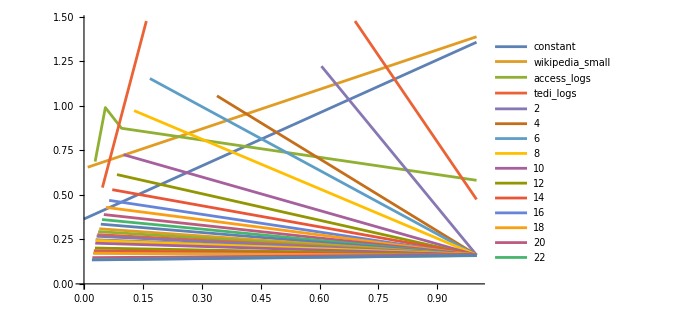

```mathematica
ListLinePlot@GroupBy[cwMacbook,(#"test_case"&)->({#"compression_ratio",#"duration"}&)]
```

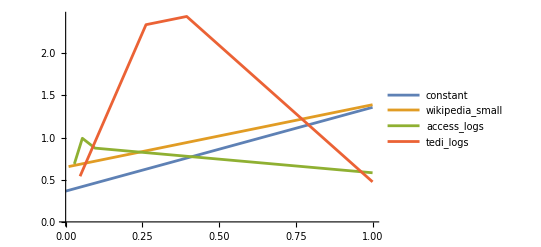

```mathematica
ListLinePlot@GroupBy[Select[cwMacbook,!StringMatchQ[#"test_case",DigitCharacter..]&],(#"test_case"&)->({#"compression_ratio",#"duration"}&)]
```